Nonlinear Breit-Wheeler pair production in collisions of bremsstrahlung γ quanta and a tightly focused laser pulse

A. Golub, S. Villalba-Chávez, and C. Mü̈ller, PHYSICAL REVIEW D 105, 116016 (2022)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2

((4/3-(4 f)/3+f^2) ℓ)/f

(-ⅇ^(-7 ℓ/9)+(1-f)^(4 ℓ/3))/(f (7/9+4/3 Log[1-f]))

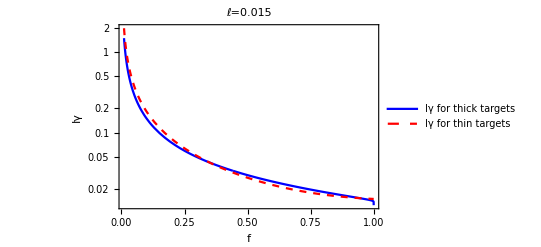

```mathematica
Clear[f,ℓ,Iγ2]
(*  *)
Iγ1=ℓ/f(4/3-(4f)/3+f^2)
(* for thicker targets with ℓ<2 *)
Iγ2=((1-f)^(4ℓ/3)-Exp[-7ℓ/9])/(f(7/9+4/3Log[1-f]))
ℓ=0.015;
LogPlot[{Iγ2,Iγ1},{f,0.01,1},PlotLegends->{"Iγ for thick targets","Iγ for thin targets"},PlotStyle->{Directive[Blue],Directive[Red,Dashed]},Frame->True,FrameLabel->{"f","Iγ"},PlotLabel->"ℓ=0.015"]
```

```mathematica
(* these distributions are not PDFs (can't be sampled from), unless truncated (due to singularities as f->0) *)
Clear[f,ℓ,Iγ2]
Iγ1=ℓ/f(4/3-(4f)/3+f^2);
(*Integrate[Iγ1,f]*)
Integrate[Iγ1,{f,0,1}]
Iγ2=((1-f)^(4ℓ/3)-Exp[-7ℓ/9])/(f(7/9+4/3Log[1-f]));
(*Integrate[Iγ2,f]*)
Integrate[Iγ2,{f,0,1}]
```

Integrate::idiv: Integral of -(4 ℓ)/3+(4 ℓ)/(3 f)+f ℓ does not converge on {0,1}.

∫_0^1 ((4/3-(4 f)/3+f^2) ℓ)/f ⅆf

Integrate::idiv: Integral of -(9 ⅇ^(-7 ℓ/9))/(f (7+12 Log[1+Times[«2»]]))+(9 (1-f)^(4 ℓ/3))/(f (7+12 Log[1+Times[«2»]])) does not converge on {0,1}.

∫_0^1 (-ⅇ^(-7 ℓ/9)+(1-f)^(4 ℓ/3))/(f (7/9+4/3 Log[1-f]))ⅆf

## Figure 3

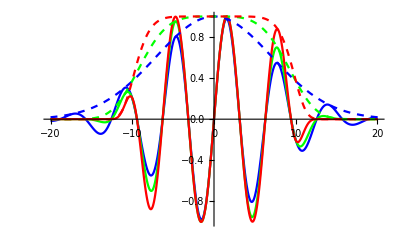

```mathematica
Clear[ϕ,Ex,n,ζ,Φ,t,z,τ,zR,W0,λ,W,r,ω,Exenv]
W0=∞;
zR=π W0^2/λ;
ζ=z/zR;
W=W0 Sqrt[1+(z/zR)^2];
r=0;
Φ= ϕ-ζ r^2/W^2+ArcTan[ζ];(*=0 since W0->∞*)
τ=5;(*[fs]*)
ω=1.55 1.6 10^-19/(1.05 10^-34) 10^-15;(*[10^15 s-1]*)
Ex=(Exp[-(Sqrt[2Log[2]]ϕ/(ω τ))^n] Exp[-(r/W)^2] Sin[Φ])/Sqrt[1+ζ^2];
Exenv=(Exp[-(Sqrt[2Log[2]]ϕ/(ω τ))^n] Exp[-(r/W)^2])/Sqrt[1+ζ^2];
Plot[{Ex/.{n->2},Ex/.{n->4},Ex/.{n->8},Exenv/.{n->2},Exenv/.{n->4},Exenv/.{n->8}},{ϕ,-20,+20},PlotRange->{-1,1},PlotStyle->{Blue,Green,Red,Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Red,Dashed]}]//Quiet
```

## Figure 4...

```mathematica
Clear[Φ,t,z,x,y,r,ω,Ex,ℰ0,ζ,W0,W,λ,zR,c,fLow]

zR=π W0^2/λ;
W=W0 Sqrt[1+ζ^2];
r=Sqrt[x^2+y^2];
ζ=z/zR;

(* eq 5 *)
Φ=ω(t-z)-ζ r^2/W^2+ArcTan[ζ];
(* eq 4 *)
Ex=ℰ0 Exp[-(Sqrt[2Log[2]](t-z)/τ)^2]/Sqrt[1+ζ^2] Exp[-(r/W)^2]Sin[Φ];

(** TABLE I parameters **)
c=3 10^8;(*[m/s]*)
ξ=70;(*[]*)
τ=10^6 c 30 10^-15;(*[μm], 30 fs *)
λ=0.8;(*[μm]*)
ω=2π c/(λ 10^-6);(*[s-1]*)
W0=2;(*[μm]*)
ℰ0=1;
fLow=Ex^2/.{y->0,t->0,z->zzR zR,x->xW0 W0}
DensityPlot[fLow,{zzR,-2,+2},{xW0,-4,+4},PlotPoints->200,PlotRange->All,AspectRatio->1/4,ColorFunction->"TemperatureMap",Frame->True,FrameLabel->{"z[zR]","x[W0]"},PlotLegends->{-4,0},ClippingStyle->Automatic]
```

1/(1+1. zzR^2)2^(-12.1847 zzR^2) ⅇ^(-(2 xW0^2)/(1+1. zzR^2)) Sin[3.7011×10^16 zzR+(1. xW0^2 zzR)/(1+1. zzR^2)-ArcTan[1. zzR]]^2

-Graphics-

## Figure 5

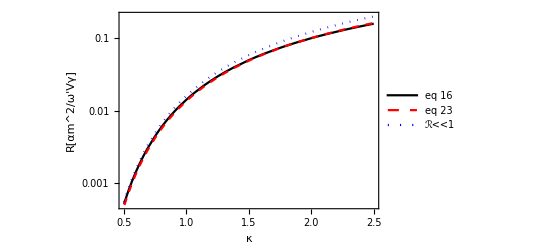

```mathematica
Clear[ℛ16,κ,u,z,ϕ,dϕ,dz]
(*1/(√π)Integrate[Cos[t^3/3+z t],{t,0,∞}]//Normal*)
ϕ[z_]:=1/(6 √π √Abs[z])(π (-z+Abs[z]) BesselJ[-1/3,2/3 Abs[z]^(3/2)]+π (-z+Abs[z]) BesselJ[1/3,2/3 Abs[z]^(3/2)]+√3 (z+Abs[z]) BesselK[-1/3,2/3 Abs[z]^(3/2)])
dz=10^-4;
dϕ[z_]:=(ϕ[z+dz]-ϕ[z-dz])/(2dz)
ℛ16[κ_?NumericQ]:=ℛ16[κ]=-1/(6√π)NIntegrate[(8u+1)/(u Sqrt[u(u-1)])dϕ[(4u/κ)^(2/3)]/(4u/κ)^(2/3),{u,1,∞}]
(* κ<<1 expansion *)
ℛll1=1/8(3/2)^(3/2) κ Exp[-8/(3κ)];
(* equation 23 *)
ℛ23=1/π(2/3)^(3/2) BesselK[7/12,4/(3κ)]BesselK[1/12,4/(3κ)];
(* plot *)
LogPlot[{ℛ16[κ],ℛ23,ℛll1},{κ,0.5,2.5},PlotStyle->{Black,Directive[Red,Dashed],Directive[Blue,Dotted]},PlotRange->{0.5 10^-3,2 10^-1},PlotPoints->2,Frame->True,FrameLabel->{"κ","R[αm^2/ω'Vγ]"},PlotLegends->{"eq 16","eq 23", "ℛ<<1"}]
```

```mathematica
(* prove eq 23 *)
Clear[κ,p]
(Sqrt[8κ]/6 Integrate[BesselK[2/3,p]/Sqrt[p-8/(3κ)],{p,8/(3κ),∞}]//Normal//Simplify)-(2/3)^(3/2)BesselK[7/12,4/(3κ)]BesselK[1/12,4/(3κ)]//FullSimplify
```

0

## Figure 13...

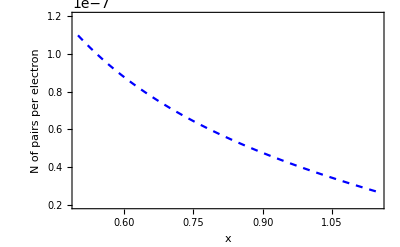

```mathematica
Clear[x]

Plot[{6 10^-8 Cot[x]},{x,0.5,1.15},PlotRange->{2 10^-8,12 10^-8},Frame->True,FrameLabel->{"x","N of pairs per electron"},PlotStyle->{{Blue,Dashed}},GridLines->{{},{4 10^-8,6 10^-8,8 10^-8,10 10^-8}}]
```

## Figure 19

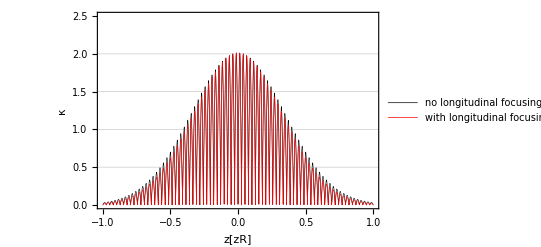

```mathematica
Clear[t,t,κ,ϕ,e]
Clear[Φ,t,z,x,y,r,ω,Ex,ℰ0,ζ,W0,W,λ,zR,c,Ex1,Ex2,ωp,ℏ,m,κ1,κ2]

ϕ=0;
x=y=0;
t=0;

zR=π W0^2/λ;
W=W0 Sqrt[1+ζ^2];
r=Sqrt[x^2+y^2];
ζ=z/zR;

(* eq 5 *)
Φ=ω(t-10^-6 z/c)-ζ r^2/W^2+ArcTan[ζ];
(* eq 4 *)
Ex1=ℰ0 Exp[-(Sqrt[2Log[2]](t-z)/τ)^2]/Sqrt[1+ζ^2] Exp[-(r/W)^2]Sin[Φ];
Ex2=ℰ0 Exp[-(Sqrt[2Log[2]](t-z)/τ)^2]/1 Exp[-(r/W)^2]Sin[Φ];

(** TABLE I parameters **)
c=3 10^8;(*[m/s]*)
e=1.6 10^-19;(*[C]*)
m=9.1 10^-31;(*[Kg]*)
ℏ=1.05 10^-34;(*[J s]*)

ξ=70;(*[]*)
τ=10^6 c 30 10^-15;(*[μm], 30 fs *)
λ=0.8;(*[μm]*)
ω=2π c/(λ 10^-6);(*[s-1]*)
W0=2;(*[μm]*)
ℰ0=ξ;(*[?](m ω ξ)/e*)

(* eq A2: what is the value of ω'? *)
ωp= 1.1221118259788085*^19;
κ1=2(ℏ ωp)/(m c^2) Abs[Ex1];
κ2=2(ℏ ωp)/(m c^2)  Abs[Ex2];

Plot[{κ2/.{z->zzR zR },κ1/.{z->zzR zR }},{zzR,-1,+1},PlotStyle->{{Black,Thickness[0.001]},{Red,Thickness[0.001]}},Frame->True,FrameLabel->{"z[zR]","κ"},GridLines->{{},{0.5,1,1.5,2}},PlotRange->{0,2.5},Axes->False,PlotLegends->{"no longitudinal focusing","with longitudinal focusing"},PlotPoints->300]
```